```mathematica
ariasD[0] = 1;
ariasD[n_Integer?Positive] := ariasD[n] = Sum[2^((k (k - 1) - n (n - 1))/2) ariasD[k]/(n - k + 1)!, {k, 0, n - 1}]/(2^n - 1);
iFabiusF[x_] := Module[{prec = Precision[x], n, p, q, s, tol, w, y, z},
  If[x < 0, Return[0, Module]]; tol = 10^(-prec);
  z = SetPrecision[x, Infinity]; s = 1; y = 0;
  z = If[0 <= z <= 2, 1 - Abs[1 - z],
    q = Quotient[z, 2];
    If[ThueMorse[q] == 1, s = -1];
    1 - Abs[1 - z + 2 q]];
  While[z > 0,
   n = -Floor[RealExponent[z, 2]]; p = 2^n;
   z -= 1/p; w = 1;
   Do[w = ariasD[m] + p z w/(n - m + 1); p /= 2, {m, n}];
   y = w - y;
   If[Abs[w] < Abs[y] tol, Break[]]];
  SetPrecision[s Abs[y], prec]]
FabiusF[Infinity] = Interval[{-1, 1}];
FabiusF[x_?NumberQ] /; If[Im[x] == 0, TrueQ[Composition[BitAnd[#, # - 1] &, Denominator][x] == 0], False] := iFabiusF[x]
Derivative[n_Integer][FabiusF] := 2^(n (n + 1)/2) FabiusF[2^n #] &
SetAttributes[FabiusF, {NumericFunction, Listable}];
```

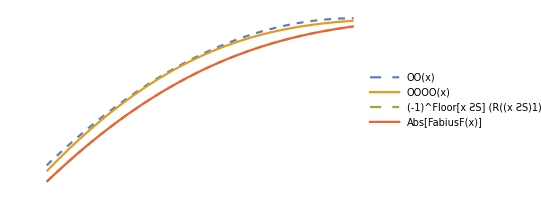
OO[3/4]= | 15/16
0.9375
OOOO[3/4]= | 0.935031
0.935031
R[3/4]= | 60985/65536
0.930557
FabiusF[3/4]= | 67/72
0.930556
{-Graphics-}

1.7043521015873016*10^6*(2.9336661100387573*10^-7-2.9336661100387573*10^-7*(-1)^FLOOR(X)+(-1)^FLOOR(X)*MAX(0,-511/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-509/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-507/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-505/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-503/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-501/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-499/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-497/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-495/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-493/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-491/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-489/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-487/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-485/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-483/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-481/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-479/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-477/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-475/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-473/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-471/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-469/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-467/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-465/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-463/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-461/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-459/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-457/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-455/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-453/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-451/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-449/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-447/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-445/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-443/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-441/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-439/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-437/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-435/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-433/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-431/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-429/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-427/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-425/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-423/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-421/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-419/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-417/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-415/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-413/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-411/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-409/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-407/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-405/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-403/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-401/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-399/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-397/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-395/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-393/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-391/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-389/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-387/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-385/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-383/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-381/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-379/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-377/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-375/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-373/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-371/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-369/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-367/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-365/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-363/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-361/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-359/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-357/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-355/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-353/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-351/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-349/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-347/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-345/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-343/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-341/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-339/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-337/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-335/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-333/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-331/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-329/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-327/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-325/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-323/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-321/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-319/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-317/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-315/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-313/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-311/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-309/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-307/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-305/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-303/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-301/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-299/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-297/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-295/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-293/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-291/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-289/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-287/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-285/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-283/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-281/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-279/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-277/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-275/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-273/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-271/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-269/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-267/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-265/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-263/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-261/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-259/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-257/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-255/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-253/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-251/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-249/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-247/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-245/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-243/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-241/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-239/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-237/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-235/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-233/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-231/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-229/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-227/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-225/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-223/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-221/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-219/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-217/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-215/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-213/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-211/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-209/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-207/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-205/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-203/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-201/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-199/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-197/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-195/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-193/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-191/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-189/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-187/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-185/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-183/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-181/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-179/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-177/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-175/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-173/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-171/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-169/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-167/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-165/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-163/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-161/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-159/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-157/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-155/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-153/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-151/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-149/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-147/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-145/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-143/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-141/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-139/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-137/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-135/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-133/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-131/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-129/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-127/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-125/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-123/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-121/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-119/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-117/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-115/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-113/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-111/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-109/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-107/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-105/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-103/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-101/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-99/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-97/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-95/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-93/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-91/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-89/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-87/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-85/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-83/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-81/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-79/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-77/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-75/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-73/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-71/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-69/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-67/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-65/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-63/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-61/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-59/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-57/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-55/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-53/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-51/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-49/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-47/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-45/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-43/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-41/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-39/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-37/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-35/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-33/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-31/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-29/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-27/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-25/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-23/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-21/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-19/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-17/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-15/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-13/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-11/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-9/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-7/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-5/512+MOD(X,1))^8-1.*(-1)^FLOOR(X)*MAX(0,-3/512+MOD(X,1))^8+(-1)^FLOOR(X)*MAX(0,-1/512+MOD(X,1))^8)

```mathematica
T=8;
A0[x_]:=(Max[x,0]^T)/T!;
A1[x_]:=2^1 (A0[x]-A0[(x-1/2^1)]);
A2[x_]:=2^2 (A1[x]-A1[(x-1/2^2)]);
A3[x_]:=2^3 (A2[x]-A2[(x-1/2^3)]);
A4[x_]:=2^4 (A3[x]-A3[(x-1/2^4)]);
A5[x_]:=2^5 (A4[x]-A4[(x-1/2^5)]);
A6[x_]:=2^6 (A5[x]-A5[(x-1/2^6)]);
A7[x_]:=2^7 (A6[x]-A6[(x-1/2^7)]);
A8[x_]:=2^8 (A7[x]-A7[(x-1/2^8)]);
A9[x_]:=2^9 (A8[x]-A8[(x-1/2^9)]);
A10[x_]:=2^10 (A9[x]-A9[(x-1/2^10)]);
A11[x_]:=2^11 (A10[x]-A10[(x-1/2^11)]);
A12[x_]:=2^12 (A11[x]-A11[(x-1/2^12)]);
A13[x_]:=2^13 (A12[x]-A12[(x-1/2^13)]);
A14[x_]:=2^14 (A13[x]-A13[(x-1/2^14)]);
A15[x_]:=2^15 (A14[x]-A14[(x-1/2^15)]);
A16[x_]:=2^16 (A15[x]-A15[(x-1/2^16)]);
A17[x_]:=2^17 (A16[x]-A16[(x-1/2^17)]);
A18[x_]:=2^18 (A17[x]-A17[(x-1/2^18)]);
A19[x_]:=2^19 (A18[x]-A18[(x-1/2^19)]);
A20[x_]:=2^20 (A19[x]-A19[(x-1/2^20)]);
A21[x_]:=2^21 (A20[x]-A20[(x-1/2^21)]);
A22[x_]:=2^22 (A21[x]-A21[(x-1/2^22)]);
A23[x_]:=2^23 (A22[x]-A22[(x-1/2^23)]);
A24[x_]:=2^24 (A23[x]-A23[(x-1/2^24)]);
A25[x_]:=2^25 (A24[x]-A24[(x-1/2^25)]);
A26[x_]:=2^26 (A25[x]-A25[(x-1/2^26)]);
A27[x_]:=2^27 (A26[x]-A26[(x-1/2^27)]);
A28[x_]:=2^28 (A27[x]-A27[(x-1/2^28)]);
A29[x_]:=2^29 (A28[x]-A28[(x-1/2^29)]);
A30[x_]:=2^30 (A29[x]-A29[(x-1/2^30)]);
A31[x_]:=2^31 (A30[x]-A30[(x-1/2^31)]);
A32[x_]:=2^32 (A31[x]-A31[(x-1/2^32)]);
R[x_]:=A8[(x-1/2^(T+1))];
ƧS=1;
RC[x_]:=(-1)^Floor[x*ƧS] (R[Mod[x*ƧS,1]]-0.5)+0.5;
(*ToUpperCase[StringReplace[StringReplace[StringReplace[ToString[R[x],InputForm],"["->"("],"]"->")"]," "-> ""]]*)
(*ToUpperCase[StringReplace[StringReplace[StringReplace[ToString[Simplify[R[x]],InputForm],"["->"("],"]"->")"]," "-> ""]]*)
OO[x_]:=(1/32)*((1-8*(x-1))*Abs[1-8*(x-1)]+(8*(x-1)+7)*Abs[8*(x-1)+7]-(8*(x-1)+5)*Abs[8*(x-1)+5]-(8*(x-1)+3)*Abs[8*(x-1)+3]+(8*(x-1)+1)*Abs[8*(x-1)+1]-(3-8*(x-1))*Abs[3-8*(x-1)]-(5-8*(x-1))*Abs[5-8*(x-1)]+(7-8*(x-1))*Abs[7-8*(x-1)]);
OOOO[x_]:=-((0-(-1)^Floor[x/1+0.]*(Exp[-(1/(x-1*Floor[x/1]))]/(Exp[-(1/(x-1*Floor[x/1]))]+Exp[-(1/(1-(x-1*Floor[x/1])))]))+(-1)^Floor[x/1+0.]*(Exp[-(1/(1-(x-1*Floor[x/1])))]/(Exp[-(1/(x-1*Floor[x/1]))]+Exp[-(1/(1-(x-1*Floor[x/1])))])))/2)+0.5;

Column[{
TableForm[{
{"OO[3/4]=" ,{OO[3/4],N[OO[3/4]]}},
{"OOOO[3/4]=" ,{OOOO[3/4],N[OOOO[3/4]]}},
{"R[3/4]=" ,{R[3/4],N[R[3/4]]}},
{"FabiusF[3/4]=" ,{FabiusF[3/4],N[FabiusF[3/4]]}}
}],
{Plot[{OO[x],OOOO[x],(-1)^Floor[x*ƧS] (R[Mod[x*ƧS,1]]-0.5)+0.5,Abs[FabiusF[x]]},{x,.75,.875},AspectRatio->1/2,ImageSize->Full,Axes->False,MaxRecursion->0,PlotPoints->1+2^8,PlotStyle->{Dashed,Normal},PlotLegends-> Placed["Expressions",{Center,Top}],PlotRangePadding->0]}},Center]
ToUpperCase[StringReplace[ToString[
Simplify[ExpandAll[
(-1)^Floor[x]*(R[Mod[x,1]]-0.5)+0.5
]]
,InputForm],{" "-> "","*^"-> "*10^","["->"(","]"->")"  }]]
(*Simplify[R[x]]*)
```

```mathematica
ToUpperCase[StringReplace[ToString[
(*Simplify[ExpandAll[*)
(-1)^Floor[x*O]*(R[Mod[x*O,1]]-0.5)+0.5
(*]]*)
,InputForm],{" "-> "","*^"-> "*10^","["->"(","]"->")"  }]]
(*Simplify[R[x]]*)
```

0.5+(-1)^FLOOR(O*X)*(-0.5+256*(-128*(-64*(-32*(-16*(-8*(-4*(-2*(-1/40320*MAX(0,-511/512+MOD(O*X,1))^8+MAX(0,-255/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-383/512+MOD(O*X,1))^8+MAX(0,-127/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-447/512+MOD(O*X,1))^8+MAX(0,-191/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-319/512+MOD(O*X,1))^8+MAX(0,-63/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-479/512+MOD(O*X,1))^8+MAX(0,-223/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-351/512+MOD(O*X,1))^8+MAX(0,-95/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-415/512+MOD(O*X,1))^8+MAX(0,-159/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-287/512+MOD(O*X,1))^8+MAX(0,-31/512+MOD(O*X,1))^8/40320))))+16*(-8*(-4*(-2*(-1/40320*MAX(0,-495/512+MOD(O*X,1))^8+MAX(0,-239/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-367/512+MOD(O*X,1))^8+MAX(0,-111/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-431/512+MOD(O*X,1))^8+MAX(0,-175/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-303/512+MOD(O*X,1))^8+MAX(0,-47/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-463/512+MOD(O*X,1))^8+MAX(0,-207/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-335/512+MOD(O*X,1))^8+MAX(0,-79/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-399/512+MOD(O*X,1))^8+MAX(0,-143/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-271/512+MOD(O*X,1))^8+MAX(0,-15/512+MOD(O*X,1))^8/40320)))))+32*(-16*(-8*(-4*(-2*(-1/40320*MAX(0,-503/512+MOD(O*X,1))^8+MAX(0,-247/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-375/512+MOD(O*X,1))^8+MAX(0,-119/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-439/512+MOD(O*X,1))^8+MAX(0,-183/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-311/512+MOD(O*X,1))^8+MAX(0,-55/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-471/512+MOD(O*X,1))^8+MAX(0,-215/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-343/512+MOD(O*X,1))^8+MAX(0,-87/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-407/512+MOD(O*X,1))^8+MAX(0,-151/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-279/512+MOD(O*X,1))^8+MAX(0,-23/512+MOD(O*X,1))^8/40320))))+16*(-8*(-4*(-2*(-1/40320*MAX(0,-487/512+MOD(O*X,1))^8+MAX(0,-231/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-359/512+MOD(O*X,1))^8+MAX(0,-103/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-423/512+MOD(O*X,1))^8+MAX(0,-167/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-295/512+MOD(O*X,1))^8+MAX(0,-39/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-455/512+MOD(O*X,1))^8+MAX(0,-199/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-327/512+MOD(O*X,1))^8+MAX(0,-71/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-391/512+MOD(O*X,1))^8+MAX(0,-135/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-263/512+MOD(O*X,1))^8+MAX(0,-7/512+MOD(O*X,1))^8/40320))))))+64*(-32*(-16*(-8*(-4*(-2*(-1/40320*MAX(0,-507/512+MOD(O*X,1))^8+MAX(0,-251/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-379/512+MOD(O*X,1))^8+MAX(0,-123/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-443/512+MOD(O*X,1))^8+MAX(0,-187/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-315/512+MOD(O*X,1))^8+MAX(0,-59/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-475/512+MOD(O*X,1))^8+MAX(0,-219/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-347/512+MOD(O*X,1))^8+MAX(0,-91/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-411/512+MOD(O*X,1))^8+MAX(0,-155/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-283/512+MOD(O*X,1))^8+MAX(0,-27/512+MOD(O*X,1))^8/40320))))+16*(-8*(-4*(-2*(-1/40320*MAX(0,-491/512+MOD(O*X,1))^8+MAX(0,-235/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-363/512+MOD(O*X,1))^8+MAX(0,-107/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-427/512+MOD(O*X,1))^8+MAX(0,-171/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-299/512+MOD(O*X,1))^8+MAX(0,-43/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-459/512+MOD(O*X,1))^8+MAX(0,-203/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-331/512+MOD(O*X,1))^8+MAX(0,-75/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-395/512+MOD(O*X,1))^8+MAX(0,-139/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-267/512+MOD(O*X,1))^8+MAX(0,-11/512+MOD(O*X,1))^8/40320)))))+32*(-16*(-8*(-4*(-2*(-1/40320*MAX(0,-499/512+MOD(O*X,1))^8+MAX(0,-243/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-371/512+MOD(O*X,1))^8+MAX(0,-115/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-435/512+MOD(O*X,1))^8+MAX(0,-179/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-307/512+MOD(O*X,1))^8+MAX(0,-51/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-467/512+MOD(O*X,1))^8+MAX(0,-211/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-339/512+MOD(O*X,1))^8+MAX(0,-83/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-403/512+MOD(O*X,1))^8+MAX(0,-147/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-275/512+MOD(O*X,1))^8+MAX(0,-19/512+MOD(O*X,1))^8/40320))))+16*(-8*(-4*(-2*(-1/40320*MAX(0,-483/512+MOD(O*X,1))^8+MAX(0,-227/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-355/512+MOD(O*X,1))^8+MAX(0,-99/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-419/512+MOD(O*X,1))^8+MAX(0,-163/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-291/512+MOD(O*X,1))^8+MAX(0,-35/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-451/512+MOD(O*X,1))^8+MAX(0,-195/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-323/512+MOD(O*X,1))^8+MAX(0,-67/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-387/512+MOD(O*X,1))^8+MAX(0,-131/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-259/512+MOD(O*X,1))^8+MAX(0,-3/512+MOD(O*X,1))^8/40320)))))))+128*(-64*(-32*(-16*(-8*(-4*(-2*(-1/40320*MAX(0,-509/512+MOD(O*X,1))^8+MAX(0,-253/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-381/512+MOD(O*X,1))^8+MAX(0,-125/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-445/512+MOD(O*X,1))^8+MAX(0,-189/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-317/512+MOD(O*X,1))^8+MAX(0,-61/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-477/512+MOD(O*X,1))^8+MAX(0,-221/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-349/512+MOD(O*X,1))^8+MAX(0,-93/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-413/512+MOD(O*X,1))^8+MAX(0,-157/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-285/512+MOD(O*X,1))^8+MAX(0,-29/512+MOD(O*X,1))^8/40320))))+16*(-8*(-4*(-2*(-1/40320*MAX(0,-493/512+MOD(O*X,1))^8+MAX(0,-237/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-365/512+MOD(O*X,1))^8+MAX(0,-109/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-429/512+MOD(O*X,1))^8+MAX(0,-173/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-301/512+MOD(O*X,1))^8+MAX(0,-45/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-461/512+MOD(O*X,1))^8+MAX(0,-205/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-333/512+MOD(O*X,1))^8+MAX(0,-77/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-397/512+MOD(O*X,1))^8+MAX(0,-141/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-269/512+MOD(O*X,1))^8+MAX(0,-13/512+MOD(O*X,1))^8/40320)))))+32*(-16*(-8*(-4*(-2*(-1/40320*MAX(0,-501/512+MOD(O*X,1))^8+MAX(0,-245/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-373/512+MOD(O*X,1))^8+MAX(0,-117/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-437/512+MOD(O*X,1))^8+MAX(0,-181/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-309/512+MOD(O*X,1))^8+MAX(0,-53/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-469/512+MOD(O*X,1))^8+MAX(0,-213/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-341/512+MOD(O*X,1))^8+MAX(0,-85/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-405/512+MOD(O*X,1))^8+MAX(0,-149/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-277/512+MOD(O*X,1))^8+MAX(0,-21/512+MOD(O*X,1))^8/40320))))+16*(-8*(-4*(-2*(-1/40320*MAX(0,-485/512+MOD(O*X,1))^8+MAX(0,-229/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-357/512+MOD(O*X,1))^8+MAX(0,-101/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-421/512+MOD(O*X,1))^8+MAX(0,-165/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-293/512+MOD(O*X,1))^8+MAX(0,-37/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-453/512+MOD(O*X,1))^8+MAX(0,-197/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-325/512+MOD(O*X,1))^8+MAX(0,-69/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-389/512+MOD(O*X,1))^8+MAX(0,-133/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-261/512+MOD(O*X,1))^8+MAX(0,-5/512+MOD(O*X,1))^8/40320))))))+64*(-32*(-16*(-8*(-4*(-2*(-1/40320*MAX(0,-505/512+MOD(O*X,1))^8+MAX(0,-249/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-377/512+MOD(O*X,1))^8+MAX(0,-121/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-441/512+MOD(O*X,1))^8+MAX(0,-185/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-313/512+MOD(O*X,1))^8+MAX(0,-57/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-473/512+MOD(O*X,1))^8+MAX(0,-217/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-345/512+MOD(O*X,1))^8+MAX(0,-89/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-409/512+MOD(O*X,1))^8+MAX(0,-153/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-281/512+MOD(O*X,1))^8+MAX(0,-25/512+MOD(O*X,1))^8/40320))))+16*(-8*(-4*(-2*(-1/40320*MAX(0,-489/512+MOD(O*X,1))^8+MAX(0,-233/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-361/512+MOD(O*X,1))^8+MAX(0,-105/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-425/512+MOD(O*X,1))^8+MAX(0,-169/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-297/512+MOD(O*X,1))^8+MAX(0,-41/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-457/512+MOD(O*X,1))^8+MAX(0,-201/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-329/512+MOD(O*X,1))^8+MAX(0,-73/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-393/512+MOD(O*X,1))^8+MAX(0,-137/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-265/512+MOD(O*X,1))^8+MAX(0,-9/512+MOD(O*X,1))^8/40320)))))+32*(-16*(-8*(-4*(-2*(-1/40320*MAX(0,-497/512+MOD(O*X,1))^8+MAX(0,-241/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-369/512+MOD(O*X,1))^8+MAX(0,-113/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-433/512+MOD(O*X,1))^8+MAX(0,-177/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-305/512+MOD(O*X,1))^8+MAX(0,-49/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-465/512+MOD(O*X,1))^8+MAX(0,-209/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-337/512+MOD(O*X,1))^8+MAX(0,-81/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-401/512+MOD(O*X,1))^8+MAX(0,-145/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-273/512+MOD(O*X,1))^8+MAX(0,-17/512+MOD(O*X,1))^8/40320))))+16*(-8*(-4*(-2*(-1/40320*MAX(0,-481/512+MOD(O*X,1))^8+MAX(0,-225/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-353/512+MOD(O*X,1))^8+MAX(0,-97/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-417/512+MOD(O*X,1))^8+MAX(0,-161/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-289/512+MOD(O*X,1))^8+MAX(0,-33/512+MOD(O*X,1))^8/40320)))+8*(-4*(-2*(-1/40320*MAX(0,-449/512+MOD(O*X,1))^8+MAX(0,-193/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-321/512+MOD(O*X,1))^8+MAX(0,-65/512+MOD(O*X,1))^8/40320))+4*(-2*(-1/40320*MAX(0,-385/512+MOD(O*X,1))^8+MAX(0,-129/512+MOD(O*X,1))^8/40320)+2*(-1/40320*MAX(0,-257/512+MOD(O*X,1))^8+MAX(0,-1/512+MOD(O*X,1))^8/40320)))))))))